## Rossler System

```mathematica
Clear[a,b,c]
f[{a_,b_,c_}][{x_,y_,z_}]:={-y-z, x +a y,b+z (x  - c)}
Df[{a_,b_,c_}][{x_,y_,z_}]=D[f[{a,b,c}][{x,y,z}],{{x,y,z}}];
MatrixForm[Df[{a,b,c}][{x,y,z}]]
```

(0 | -1 | -1
1 | a | 0
z | 0 | -c+x)

Numerical solution with standard parameters.

```mathematica
y0=10RandomReal[{-1,1},3];

TMax=123;
{a,b,c}={0.2,0.2,14};
{ySol,JSol}=NDSolveValue[{
y'[t]==f[{a,b,c}][y[t]],y[0]==y0,
J'[t]==Df[{a,b,c}][y[t]].J[t],
J[0]==IdentityMatrix[3]
}, {y,J}, {t, 0 ,TMax}];
```

### Basic Plots

```mathematica
BasicPic=ParametricPlot3D[ySol[t],{t,0, TMax},PlotRange->All,PlotPoints->10^3,PlotStyle->Thin]
```

-Graphics3D-

```mathematica
?ListPointPlot3D[
```

```mathematica
t=23;
ListPointPlot3D[Table[ ySol[s],{s, 0,t,0.1}]]
```

-Graphics3D-

```mathematica
Manipulate[
Show[
BasicPic,
ListPointPlot3D[Table[ ySol[s],{s, 0,t,0.1}],PlotStyle->Red]] ,
{t, 0,  TMax,0.1}]
```

ListPointPlot3D::ldata: 
   {ySol[0.], ySol[0.1], ySol[0.2], ySol[0.3], ySol[0.4], ySol[0.5], 
     ySol[0.6], ySol[0.7], ySol[0.8], ySol[0.9], <<495>>, ySol[50.5], 
     ySol[50.6], ySol[50.7], ySol[50.8], ySol[50.9]} is not a valid dataset or
     list of datasets.

Show::gcomb: Could not combine the graphics objects in 
    Show[BasicPic, ListPointPlot3D[{ySol[0.], ySol[0.1], ySol[0.2], 
       ySol[0.3], ySol[0.4], ySol[0.5], ySol[0.6], ySol[0.7], <<498>>, 
       ySol[50.6], ySol[50.7], ySol[50.8], ySol[50.9]}, <<1>>]].

### Sensitivity Plot

```mathematica
TabView[{
"plain"->Plot[SingularValueList[JSol[t]],{t, 0, TMax},PlotRange->All],
"log"->LogPlot[SingularValueList[JSol[t]],{t, 0, TMax},PlotRange->All]
}]
```

12

### Changing the Parameters

Numerical solution with different parameters. Looks like it joins back up again!

```mathematica
(*y0=10 RandomReal[{-1,1},3];*)
y0={3.1541728786927603,9.141968170249362,5.428465412696073};
TMax=32;
{a,b,c}={0.05,0.2,14};
{ySol,JSol}=NDSolveValue[{
y'[t]==f[{a,b,c}][y[t]],y[0]==y0,
J'[t]==Df[{a,b,c}][y[t]].J[t],
J[0]==IdentityMatrix[3]
}, {y,J}, {t, 0 ,TMax}];
```

Looks as though there is an attractive periodic solution that winds round once before it repeats.

```mathematica
TStart=25;
TabView[{
"3D"->Show[
ParametricPlot3D[ySol[t],{t,0, TMax},PlotRange->All,PlotPoints->10^3,AxesLabel->{"x","y","z"},
PlotStyle->{Red, Thin}],
ParametricPlot3D[ySol[t],{t,TStart, TMax},PlotRange->All,PlotPoints->10^3,AxesLabel->{"x","y","z"}]],
"3 fun"->Plot[ySol[t],{t,TStart, TMax},
AxesLabel->{"t"," "}],
"y_3"->LogPlot[ySol[t]⟦3⟧,{t,TStart, TMax},
AxesLabel->{"t","y_3"},PlotRange->All],
"log ||y(T)-y(t)(||)^2"->LogPlot[
Norm[ySol[t]-ySol[TMax]]^2,{t,TStart, TMax},
AxesLabel->{"t"," "},
PlotRange->All]
}]
```

1234

Our goal is to compute this periodic orbit.  We want to find y and T so that 
	g(y)=y(T,y)-y=0
Our Newton method approximation is 
	 g(y)≈g(y_0)+∇g(y_0).(y-y_0)=0
with y_0 a reasonable guess at a point on the periodic solution and T a reasonable guess at the period. Our Newton’s method iteration is 
	y_1=y_0-∇(g(y_0))^-1g(y_0)
where clearly
	∇g(y)=∇_y y(T,y_0)-I_3=J(T)-I_3

#### Initial Guess

We need to mess around a bit to find a reasonable guess at the period

```mathematica
TStart=25.85;
ParametricPlot3D[ySol[t],{t,TStart, TMax},PlotRange->All,PlotPoints->10^3,AxesLabel->{"x","y","z"},
PlotLabel->TMax-TStart]
ySol[TMax]
```

-Graphics3D-

{-6.89484,14.6839,0.00994699}

Just check that we have a reasonable guess.

```mathematica
T0=6.15;
y0=ySol[TMax];
{ySol0,JSol0}=NDSolveValue[{
y'[t]==f[{a,b,c}][y[t]],y[0]==y0,
J'[t]==Df[{a,b,c}][y[t]].J[t],
J[0]==IdentityMatrix[3]
}, {y,J}, {t, 0 ,T0}];
Show[
ParametricPlot3D[ySol0[t],{t, 0, T0},
PlotRange->All],
Graphics3D[ {Opacity[0.5],
Polygon[{{0,0,0},{0,0,5},{20,20,5},{20,20,0}}]
}]
]
```

-Graphics3D-

The problem is that there are two things (the initial point and the period) at the same time! There is a clever idea (stick a plane into the problem) that gets rid of the time and reduces the dimension of the root finding.  If an orbit repeatedly goes through a Poincare Section (in the simples case a plane) then it is a periodic orbit!

#### Poincare Section

Most ODE Solvers can detect when something happens! Here is the Mathematica version triggering on a plane.

```mathematica
TMax=123;
NDSolveValue[{
y'[t]==f[{a,b,c}][y[t]],y[0]==y0,
J'[t]==Df[{a,b,c}][y[t]].J[t],
J[0]==IdentityMatrix[3]
}, {y,J}, {t, 0 ,TMax},
Method->{"EventLocator",
"Event"->y[t].{1,-1,0},
"Direction"->-1,
"EventAction":>Print["y'[",t"]= ",y[t]]}];
```

y'[5.02927 ]= {11.5183,11.5183,2.61893}

y'[11.2227 ]= {11.3086,11.3086,4.34078}

y'[17.421 ]= {11.5025,11.5025,2.83855}

y'[23.6146 ]= {11.3358,11.3358,4.17454}

y'[29.8123 ]= {11.4893,11.4893,2.98915}

y'[36.0062 ]= {11.355,11.355,4.05245}

y'[42.2035 ]= {11.4785,11.4785,3.1007}

y'[48.3977 ]= {11.3693,11.3693,3.95865}

y'[54.5946 ]= {11.4695,11.4695,3.18674}

y'[60.789 ]= {11.3803,11.3803,3.88467}

y'[66.9856 ]= {11.4621,11.4621,3.2547}

y'[73.1802 ]= {11.3889,11.3889,3.82537}

y'[79.3767 ]= {11.4559,11.4559,3.30919}

y'[85.5714 ]= {11.3957,11.3957,3.77734}

y'[91.7677 ]= {11.4508,11.4508,3.3533}

y'[97.9626 ]= {11.4012,11.4012,3.73819}

y'[104.159 ]= {11.4465,11.4465,3.38923}

y'[110.354 ]= {11.4057,11.4057,3.70612}

y'[116.55 ]= {11.443,11.443,3.41862}

y'[122.745 ]= {11.4093,11.4093,3.67978}

We really want to be able to plot these points.

```mathematica
TMax=123;
{junk,Data}=Reap[
{ySol,JSol}=NDSolveValue[{
y'[t]==f[{a,b,c}][y[t]],y[0]==y0,
J'[t]==Df[{a,b,c}][y[t]].J[t],
J[0]==IdentityMatrix[3]
}, {y,J}, {t, 0 ,TMax},
Method->{"EventLocator",
"Event"->y[t].{1,-1,0},
(*"Direction"->1,*)
"EventAction":>Sow[{t,y[t]}]}];
]
```

{Null,{{{1.92569,{-11.7821,-11.7821,0.00763156}},{5.02927,{11.5183,11.5183,2.61893}},{8.14365,{-12.2153,-12.2153,0.00750508}},{11.2227,{11.3086,11.3086,4.34078}},{14.3205,{-11.8468,-11.8468,0.00761239}},{17.421,{11.5025,11.5025,2.83855}},{20.5332,{-12.1789,-12.1789,0.00751554}},{23.6146,{11.3358,11.3358,4.17454}},{26.714,{-11.889,-11.889,0.00759996}},{29.8123,{11.4893,11.4893,2.98915}},{32.923,{-12.1517,-12.1517,0.00752338}},{36.0062,{11.355,11.355,4.05245}},{39.1067,{-11.9192,-11.9192,0.00759109}},{42.2035,{11.4785,11.4785,3.1007}},{45.3131,{-12.1304,-12.1304,0.0075295}},{48.3977,{11.3693,11.3693,3.95865}},{51.4991,{-11.9421,-11.9421,0.00758437}},{54.5946,{11.4695,11.4695,3.18674}},{57.7034,{-12.1134,-12.1134,0.00753445}},{60.789,{11.3803,11.3803,3.88467}},{63.8911,{-11.9598,-11.9598,0.00757919}},{66.9856,{11.4621,11.4621,3.2547}},{70.0938,{-12.0997,-12.0997,0.00753844}},{73.1802,{11.3889,11.3889,3.82537}},{76.2829,{-11.9738,-11.9738,0.00757504}},{79.3767,{11.4559,11.4559,3.30919}},{82.4843,{-12.0884,-12.0884,0.00754168}},{85.5714,{11.3957,11.3957,3.77734}},{88.6745,{-11.9851,-11.9851,0.00757176}},{91.7677,{11.4508,11.4508,3.3533}},{94.8749,{-12.0792,-12.0792,0.00754437}},{97.9626,{11.4012,11.4012,3.73819}},{101.066,{-11.9941,-11.9941,0.00756915}},{104.159,{11.4465,11.4465,3.38923}},{107.266,{-12.0716,-12.0716,0.00754657}},{110.354,{11.4057,11.4057,3.70612}},{113.457,{-12.0015,-12.0015,0.00756698}},{116.55,{11.443,11.443,3.41862}},{119.656,{-12.0653,-12.0653,0.00754837}},{122.745,{11.4093,11.4093,3.67978}}}}}

### Newton Iteration

{5.82958,15.6037,0.247208}

{5.82931,15.6038,0.247046}

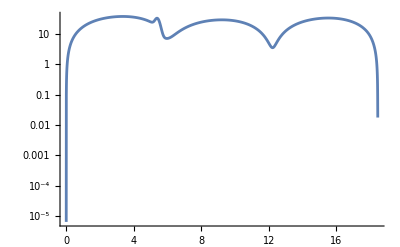

```mathematica
T0=
y1=yp-LinearSolve[JSol[Tp]-IdentityMatrix[3],ySolp[Tp]-yp]
Δ=0.001;
{ySolp1,JSolp1}=NDSolveValue[{
y'[t]==f[{a,b,c}][y[t]],y[0]==y1,
J'[t]==Df[{a,b,c}][y[t]].J[t],
J[0]==IdentityMatrix[3]
}, {y,J}, {t, 0 ,Tp+Δ},
PrecisionGoal->20];
LogPlot[ Norm[y1-ySolp1[t]],{t, 0, Tp+Δ},PlotRange->All]
```

```mathematica
y1=yp-
```

{5.82941,15.6038,0.247104}

This looks pretty close.

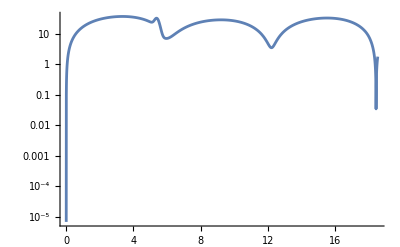

```mathematica
Δ=0.1;
{ySolp1,JSolp1}=NDSolveValue[{
y'[t]==f[{a,b,c}][y[t]],y[0]==y1,
J'[t]==Df[{a,b,c}][y[t]].J[t],
J[0]==IdentityMatrix[3]
}, {y,J}, {t, 0 ,Tp+Δ}];
LogPlot[ Norm[y1-ySolp1[t]],{t, 0, Tp+Δ},PlotRange->All]
```

```mathematica
ParametricPlot3D[ySolp1[t],{t, 0,Tp},PlotRange->All,
PlotLabel->{ySolp1[Tp]-yp}]
```

-Graphics3D-

```mathematica
tMin=t/.FindRoot[g'[t]==0,{t,161.5}]
g[tMin]
ParametricPlot3D[ySol[t],{t,tMin+0.05, TMax},PlotRange->All,PlotPoints->10^3,AxesLabel->{"x","y","z"}]
```

161.539

1.11186×10^-9

-Graphics3D-

```mathematica
{t->161.53942721802423}
```

```mathematica
2
```

170.612

{60.026,{t→167.465}}

InterpolatingFunction::dmval: Input value {204.5} lies outside the range of data in the interpolating function. Extrapolation will be used.

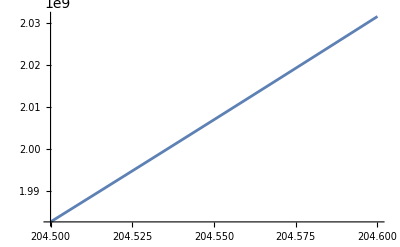

```mathematica
tMin=t/.FindRoot[dg[t]==0,{t, 170}]
FindMinimum[g[t],{t, 170}]
LogPlot[g[t],{t, 0.8 TMax, TMax}];
Plot[g[t],{t, 204.5, 204.6},PlotRange->All,PlotPoints->10^3]
```

204.008

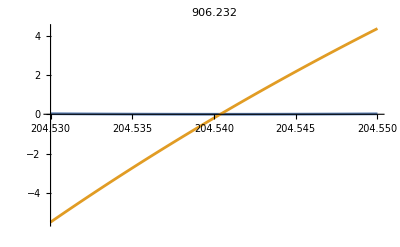

```mathematica
Plot[{g[t],dg[t]},{t, 204.53,204.55},
Prolog->{Red,PointSize[0.02],Point[{tMin,g[tMin]}]},
PlotLabel->g[tMin]
]
```

```mathematica
?FindRoot
```

```mathematica
g[204.809]
```

9.60444

```mathematica
?FindMinimum
```

```mathematica
g[0.1]
```

199.095

```mathematica
Evaluate[dg[t]]
```

2 {-9.74649-InterpolatingFunction[{{0., 223.}}, <>][t],-5.0321-InterpolatingFunction[{{0., 223.}}, <>][t],0.00835523-InterpolatingFunction[{{0., 223.}}, <>][t]}.(-InterpolatingFunction[{{0., 223.}}, <>][t])

```mathematica
?FindRoot
```

```mathematica
dg[0.1]
```

-292.801